```mathematica
SetDirectory[NotebookDirectory[]];
```

## Uloha 1 - Nystorm

### A

{{x→Function[{t},ArcTan[16 t]]}}

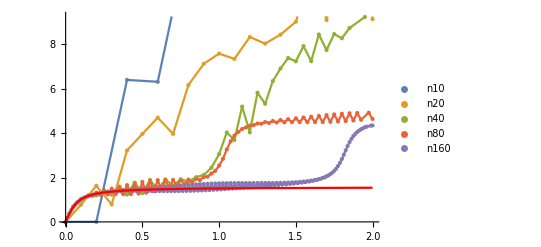

```mathematica
n10 = Import["./outputs/uloha1_a_nystrom_10n.csv","CSV"];
n20 = Import["./outputs/uloha1_a_nystrom_20n.csv","CSV"];
n40 = Import["./outputs/uloha1_a_nystrom_40n.csv","CSV"];
n80 = Import["./outputs/uloha1_a_nystrom_80n.csv","CSV"];
n160 = Import["./outputs/uloha1_a_nystrom_160n.csv","CSV"];
DSolve[{x'[t]==16 Cos[x[t]]^2, x[0]==0},x,{t,0,2}]
Show[
ListPlot[{n10, n20, n40, n80, n160}, PlotLegends->{"n10","n20","n40","n80","n160"}],
ListLinePlot[{n10, n20, n40, n80, n160}],
Plot[Evaluate[x[t]/.%],{t,0,2}, PlotStyle->Red, PlotRange->All]
]
```

### B

{{x→Function[{t},ⅇ^(-10 t)]}}

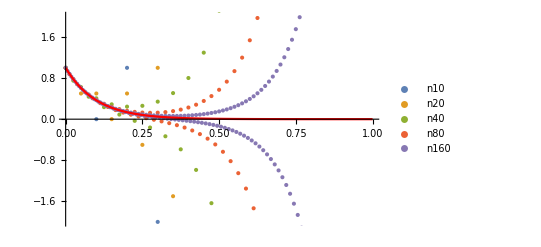

```mathematica
n10 = Import["./outputs/uloha1_b_nystrom_10n.csv","CSV"];
n20 = Import["./outputs/uloha1_b_nystrom_20n.csv","CSV"];
n40 = Import["./outputs/uloha1_b_nystrom_40n.csv","CSV"];
n80 = Import["./outputs/uloha1_b_nystrom_80n.csv","CSV"];
n160 = Import["./outputs/uloha1_b_nystrom_160n.csv","CSV"];
DSolve[{x'[t]==-10x[t], x[0]==1},x,{t,0,1}]
Show[
ListPlot[{n10, n20, n40, n80, n160}, PlotLegends->{"n10","n20","n40","n80","n160"}, PlotRange->{-2,2}],
(*ListLinePlot[{n10, n20, n40, n80, n160}],*)
Plot[Evaluate[x[t]/.%],{t,0,1}, PlotStyle->Red, PlotRange->All]
]
```

## Uloha 2 - Adams-Bashforth

{{x→Function[{t},ArcTan[16 t]]}}

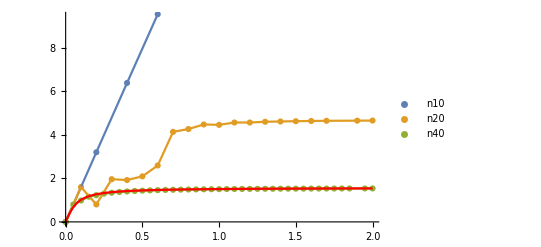

```mathematica
n10 = Import["./outputs/uloha2_adam_bash_10n.csv","CSV"];
n20 = Import["./outputs/uloha2_adam_bash_20n.csv","CSV"];
n40 = Import["./outputs/uloha2_adam_bash_40n.csv","CSV"];
n80 = Import["./outputs/uloha2_adam_bash_80n.csv","CSV"];
n160 = Import["./outputs/uloha2_adam_bash_160n.csv","CSV"];
DSolve[{x'[t]==16 Cos[x[t]]^2, x[0]==0},x,{t,0,2}]
Show[
ListPlot[{n10, n20, n40}, PlotLegends->{"n10","n20","n40","n80"}],
ListLinePlot[{n10, n20, n40}],
Plot[Evaluate[x[t]/.%],{t,0,2}, PlotStyle->Red, PlotRange->All]
]
```

## Uloha 3

### Heu

{{x→Function[{t},√(-1+2 ⅇ^t)]}}

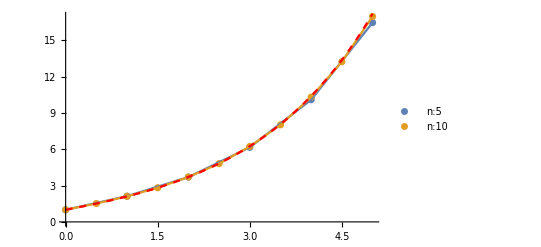

```mathematica
n5 = Import["./outputs/uloha3_heu_5n.csv","CSV"];
n10 = Import["./outputs/uloha3_heu_10n.csv","CSV"];
(*n20 = Import["./outputs/uloha3_heu_20n.csv","CSV"];
n40 = Import["./outputs/uloha3_heu_40n.csv","CSV"];
n80 = Import["./outputs/uloha3_heu_80n.csv","CSV"];*)
DSolve[{x'[t]==(x[t]^2+1)/(2x[t]), x[0]==1},x,{t,0,5}]
Show[
ListPlot[{n5, n10},PlotLegends->{"n:5", "n:10"}],
ListLinePlot[{n5, n10}],
Plot[Evaluate[x[t]/.%],{t,0,5}, PlotStyle->{Dashed, Red}, PlotRange->All]
]
```

### Heu vs Explicit Euler

{{x→Function[{t},√(-1+2 ⅇ^t)]}}

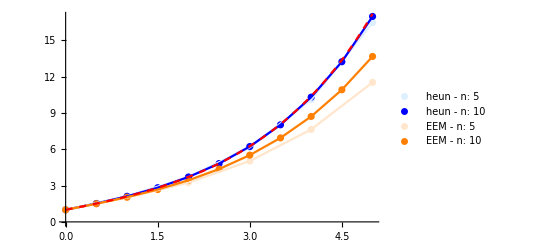

```mathematica
n5 = Import["./outputs/uloha3_heu_5n.csv","CSV"];
n10 = Import["./outputs/uloha3_heu_10n.csv","CSV"];
EE5 = Import["./outputs/uloha3_eul_5n.csv","CSV"];
EE10 = Import["./outputs/uloha3_eul_10n.csv","CSV"];
DSolve[{x'[t]==(x[t]^2+1)/(2x[t]), x[0]==1},x,{t,0,5}]
Show[
ListPlot[{n5, n10, EE5, EE10}, PlotLegends->{"heun - n: 5", "heun - n: 10","EEM - n: 5", "EEM - n: 10"}, PlotStyle->{LightBlue, Blue, LightOrange, Orange}],
ListLinePlot[{n5, n10, EE5, EE10},PlotStyle->{LightBlue, Blue, LightOrange, Orange}],
Plot[Evaluate[x[t]/.%],{t,0,5}, PlotStyle->{Red, Dashed}, PlotRange->All]
]
```

## Uloha 4

```mathematica
Solve[{1+x /2 +(x)^2 /6+(x)^3/24 == 0}, x]
```

{{x→Root-2.79Root[24+12 #1+4 #1^2+#1^3&,1]-2.7852935634052813},{x→Root-0.607-2.87 ⅈRoot[24+12 #1+4 #1^2+#1^3&,2]-0.6073532182973577},{x→Root-0.607+2.87 ⅈRoot[24+12 #1+4 #1^2+#1^3&,3]-0.6073532182973577}}

```mathematica
Solve[{-1-x -(x)^2 /2-(x)^3/6-x^4/24 ==1}, x]
```

{{x→Root-2.22-1.69 ⅈRoot[48+24 #1+12 #1^2+4 #1^3+#1^4&,1]-2.219446891977491},{x→Root-2.22+1.69 ⅈRoot[48+24 #1+12 #1^2+4 #1^3+#1^4&,2]-2.219446891977491},{x→Root0.219-2.48 ⅈRoot[48+24 #1+12 #1^2+4 #1^3+#1^4&,3]0.21944689197749137},{x→Root0.219+2.48 ⅈRoot[48+24 #1+12 #1^2+4 #1^3+#1^4&,4]0.21944689197749137}}